#### Example 4

Cálculo del field of values

-Graphics-

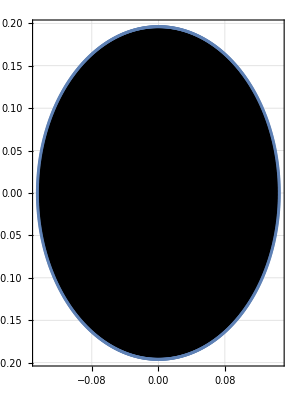

```mathematica
n=100;
x0=0;
xf=1;
dk=(xf-x0)/n;
(*Definición de matrices*)
coef1=Table[0,n-3];
coef1=Prepend[coef1,1];
coef1=Prepend[coef1,-2];
A=1.0/dk^2*ToeplitzMatrix[coef1];

sol[t_,x_]=Sin[1.0*Pi*x];
malla=Table[x0+i*dk,{i,1,n-1}];
mallaS=Table[sol[t,malla[[i]]],{i,1,n-1}];
mat=DiagonalMatrix[-Delete[mallaS,Length[mallaS]],1];
Clear[i]
For[i=1,i<n-1,i++;
aux=mallaS[[i]];
mat[[i,i-1]]=aux;
];
B=1/(2*dk)*mat;

(*Código F()*)
RangNum[matriz_?SquareMatrixQ,t_?NumericQ]/;Internal`EffectivePrecision[matriz]<∞||InexactNumberQ[t]:=Module[{tm,v},tm=(#+ConjugateTranspose[#])/2&[matriz Exp[I t]];
v=Quiet[Check[First[Eigenvectors[tm,1,Method->{"Arnoldi","Criteria"->"RealPart"}]],MaximalBy[Transpose[Eigensystem[tm]],First][[1,-1]],Eigenvectors::arall]];
(Conjugate[v].matriz.v)/(Conjugate[v].v)];

fovOut[A_,k_]:=Module[{valPropA,θ,H,λ,δ,q,j,verticesOut = {}},
valPropA =Eigenvalues[A];
(*Cálculo de F(A) si A es hermitiana*)
If[A== ConjugateTranspose[A], 
Show[Region[ConvexHullRegion[{ReIm[Max[valPropA]],ReIm[Min[valPropA]]}, Frame->True,GridLines->Automatic,   GridLinesStyle->Dashed]], ListPlot[ReIm[valPropA]]],
(*Cálculo de F(A) si A es normal*)
  If[ A . ConjugateTranspose[A] == ConjugateTranspose[A] . A, 
    Show[Region[ConvexHullRegion[ReIm[valPropA], Frame->True,GridLines->Automatic,   GridLinesStyle->Dashed]], ListPlot[ReIm[valPropA]]],
(*Cálculo de Subscript[F, Out](A,Δ)*)
θ[i_]:= (i-1)(2 Pi /k); 
H[i_]:=N[(1/2.) (E^(I θ[i]) A + ConjugateTranspose[ E^(I θ[i]) A])];
λ[i_]:= Max[Eigenvalues[H[i]]];
δ[i_]:=θ[i+1]-θ[i];
q[i_]:= E^(-I θ[i]) (λ[i]+(λ[i] Cos[δ[i]]- λ[i+1])/Sin[δ[i]] I);
For[j=1, j<=k, j++, AppendTo[verticesOut, q[j]]];

Show[Region[ConvexHullRegion[ReIm[verticesOut], Frame->True,GridLines->Automatic,   GridLinesStyle->Red]], ListPlot[ReIm[verticesOut]]
]]]];

M=Inverse[A].B;
autovalores=Eigenvalues[N[M]];
v=Table[ReIm[RangNum[M,t]],{t,0,2Pi}];
vect=AppendTo[v,ReIm[RangNum[M,0]]];
FAB=ListLinePlot[vect,Joined->True,PlotStyle->Blue,Filling->Axis];
 FAB2=fovOut[ M,1000]; 

circ=ParametricPlot[ReIm[E^(I*t)],{t,0,2 π},PlotStyle->Orange,PlotLegends->Placed[LineLegend[{Blue, Orange},{"F(A^-1B(z_-m))","D(0,1)"}],{0.75,0.0}], PlotRange->All];
Show[circ,FAB2]
FAB2
```

Valor de r para el Teorema 24: 0.196

```mathematica
r=0.196;
```

Cálculo restricción tamaño de paso h: Como el valor de r es menor al 1/3 nos encontramos en la región de estabilidad incondicional tal que para cualquier tamaño de paso, la aproximación de la solución devuelta es buena para el IMEX BDF2. En el IMEX BDF3 la restricción de tamaño de paso viene dada por lo siguiente:

```mathematica
20/(3*Max[Abs[Eigenvalues[A]]]*(7*r-1))
```

0.000448139

Resolución del problema IMEX BDF2

```mathematica
(*Datos iniciales*)
x0=0;
xf=1;
n=100;
t0=0;
tf=20;
τ=1;

h=0.1; (*Esto es lo único que se modifica de los datos iniciales*)

m=τ/h;
k=(xf-x0)/n;
nf=Round[(tf-t0)/h];

(*Construcción matriz A*)
coef1=Table[0,n-3];
coef1=Prepend[coef1,1];
coef1=Prepend[coef1,-2];
A=1/k^2*ToeplitzMatrix[coef1];
(*Construcción    g   *)

sol[t_,x_]=Sin[Pi*x];
malla=Table[x0+i*k,{i,1,n-1}];
mallaS=Table[sol[t,x0+i*k],{i,1,n-1}];

deltax=1/n;
U=Array[u,n-1];
g[U_]:=Table[   U[[i]]*Which[i==1,( U[[i+1]]-0)/(2*deltax), 1<i<n-1,( U[[i+1]]-U[[i-1]])/(2*deltax), i==n-1, ( 0-U[[i-1]])/(2*deltax) ] ,{i,n-1}];


(*Definición ftilde*)
FTilde[t_,x_]:=10*x(1-x)(1+x*Sin[t*x]);


(*Definición condiciones iniciales*)
BDF2={};
For[j=0,j≤m+1,j++;
tt=Table[N[sol[t0+(-m-1+j-1)*h,malla[[i]]]],{i,1,n-1}];

BDF2=AppendTo[BDF2,{t0+(-m-1+j-1)*h,tt}];
];
BDF2;(*Hasta aquí es la tabla que tiene los valores de t_{n-m-1} hasta t_0*)
y0=Last[BDF2][[2]];(*Establecemos la condición inicial para t=0, y los puntos x de la malla*)


(*Método*)
listasol={tt};
For[i=1,i≤nf,i++;

yMenos1=BDF2[[Length[BDF2]-1,2]];
yMenosM=BDF2[[Length[BDF2]-m,2]];
yMenosM1=BDF2[[Length[BDF2]-m-1,2]];
ListaFTilde={};
For[d=1,d≤Length[malla],d++;
ttt=FTilde[t0+h,malla[[d-1]]];
ListaFTilde=AppendTo[ListaFTilde,ttt]
];




If[t0-τ≤ 0,
y1=N[Inverse[3/2*IdentityMatrix[n-1]-h*A].(2*y0-1/2*yMenos1+h*(2*g[yMenosM]-g[yMenosM1])+h*ListaFTilde)],y1=N[Inverse[3/2*IdentityMatrix[n-1]-h*A].(2*y0-1/2*yMenos1+h*(2*g[yMenosM]-g[yMenosM1])+h*ListaFTilde)]
];


BDF2=AppendTo[BDF2,{t0+h,y1}];

lista=Table[y1[[i]],{i,1,n-1}];
listasol=AppendTo[listasol,lista];
t0=t0+h;
y0=y1;
];
ListPlot3D[listasol,DataRange->{{x0,xf},{0,tf}},PlotRange->All]
```

-Graphics3D-

Resolución del problema IMEX BDF3

```mathematica
Clear[k];

(*Datos iniciales*)
x0=0;
xf=1;
n=100;
t0=0;
tf=20;
τ=1;

h=0.1; (*Esto es lo único que se modifica de los datos iniciales*)

m=τ/h;
k=(xf-x0)/n;
nf=Round[(tf-t0)/h];

(*Construcción matriz A*)
coef1=Table[0,n-3];
coef1=Prepend[coef1,1];
coef1=Prepend[coef1,-2];
A=1/k^2*ToeplitzMatrix[coef1];
(*Construcción    g   *)

sol[t_,x_]=Sin[Pi*x];
malla=Table[x0+i*k,{i,1,n-1}];
mallaS=Table[sol[t,x0+i*k],{i,1,n-1}];

deltax=1/n;
U=Array[u,n-1];
g[U_]:=Table[   U[[i]]*Which[i==1,( U[[i+1]]-0)/(2*deltax), 1<i<n-1,( U[[i+1]]-U[[i-1]])/(2*deltax), i==n-1, ( 0-U[[i-1]])/(2*deltax) ] ,{i,n-1}];


(*Definición ftilde*)
FTilde[t_,x_]:=10*x(1-x)(1+x*Sin[t*x]);

(*Definición condiciones iniciales*)
BDF3={};
For[j=-1,j≤m+1,j++;
tt=Table[N[sol[t0+(-m-1+j-1)*h,malla[[i]]]],{i,1,n-1}];

BDF3=AppendTo[BDF3,{t0+(-m-1+j-1)*h,tt}];
];
BDF3;(*Hasta aquí es la tabla que tiene los valores de t_{n-m-1} hasta t_0*)
y0=Last[BDF3][[2]];(*Establecemos la condición inicial para t=0, y los puntos x de la malla*)


(*Método*)
listasol={tt};
For[i=1,i≤nf,i++;

yMenos1=BDF3[[Length[BDF3]-1,2]];
yMenos2=BDF3[[Length[BDF3]-2,2]];
yMenosM=BDF3[[Length[BDF3]-m,2]];
yMenosM1=BDF3[[Length[BDF3]-m-1,2]];
yMenosM2=BDF3[[Length[BDF3]-m-2,2]];
ListaFTilde={};
For[d=1,d≤Length[malla],d++;
ttt=FTilde[t0+h,malla[[d-1]]];
ListaFTilde=AppendTo[ListaFTilde,ttt]
];


If[t0-τ≤ 0,
y1=N[Inverse[11/6*IdentityMatrix[n-1]-h*A].(3*y0-3/2*yMenos1+1/3*yMenos2+h*(3*g[yMenosM]-3*g[yMenosM1]+g[yMenosM2])+h*ListaFTilde)],y1=N[Inverse[11/6*IdentityMatrix[n-1]-h*A].(3*y0-3/2*yMenos1+1/3*yMenos2+h*(3*g[yMenosM]-3*g[yMenosM1]+g[yMenosM2])+h*ListaFTilde)]
];


BDF3=AppendTo[BDF3,{t0+h,y1}];

lista=Table[y1[[i]],{i,1,n-1}];
listasol=AppendTo[listasol,lista];
t0=t0+h;
y0=y1;
];
ListPlot3D[listasol,DataRange->{{x0,xf},{0,tf}},PlotRange->All]
```

-Graphics3D-